---------------------------------------------
-----------------Question 1-----------------
---------------------------------------------

Probability Density Functions For |ψ_n(x)|^2 In 1D

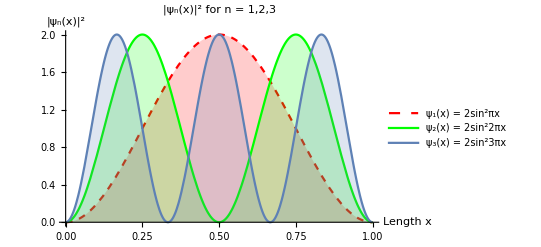

Density Functions for ψ_n(x)ψ_n(y)

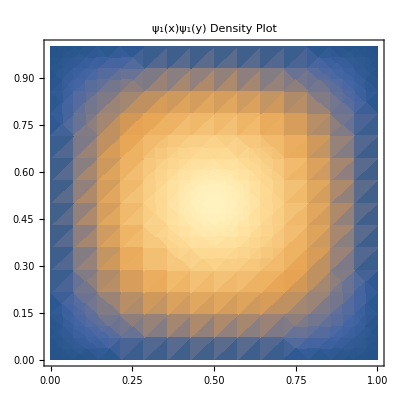

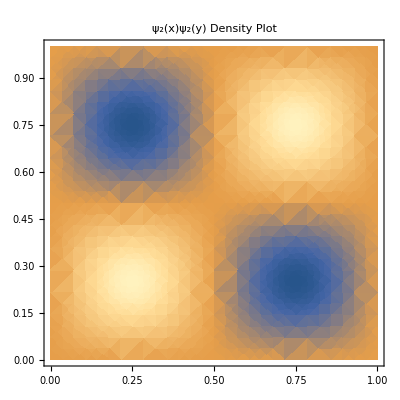

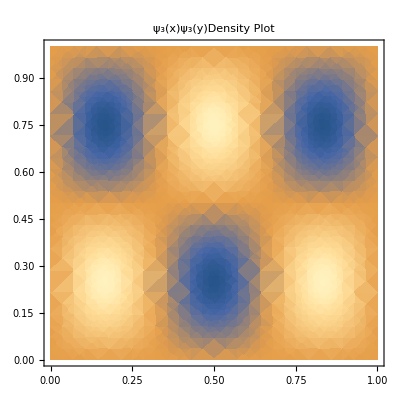

---------------------------------------------
-----------------Question 2-----------------
---------------------------------------------

Derive <x>

(1) Steps 2-3 are the human intuition steps needed before Mathematica:

(2) sin^2(nπx/L) =(1  -  cos (FractionBox[nπx, L]))/2 in the integrand of <x> = 2/L∫xsin^2(nπx/L)dx 
from the double angle identity

(3) Then the sum of two integrals can be used to solve for <x> 
such that <x> =1/L[∫xdx + ∫cos(nπx/L)dx]

(4) Given steps 2-3, I will use Mathematica to evaluate the integrals
∫xdx and ∫cos(nπx/L)dx] separately if 'n' is any positive integer on the interval
x = 0 to x = L

(5) From mathematica, '1/L * L^2/2 + (L Sin[n π])/(n π)' is <x>.

(6) <x> = L/2

Derive <p_x>

(1) Since (p̂)_x = -iℏd/dx, then <p_x> = -iℏ∫√(2/L)sin(nπx/L)d/dx√(2/L)sin(nπx/L)dx
simplifies to <p_x> = -iℏ(2  nπ)/L^2∫sin(nπx/L)cos(nπx/L)dx

(2) Using mathematica to evaluate the second integral from
step 1 on 
x = 0 to x = L where n is an element of the set of positive integers, then 
<p_x> = -iℏ(2  nπ)/L^2∫sin(nπx/L)cos(nπx/L) = -iℏ(2  nπ)/L^2*(L Sin[n π]^2)/(2 n π)
(3) Therefore, <p_x> = 0

Derive <x^2> For (σ^2)_x

(1) σ_x = √((σ^2)_x) = √(<SuperscriptBox[x, 2]> - <xSuperscriptBox[>, 2]). Therefore, I must derive <x^2> first
before calculating σ_x.

(2) <x^2> = 2/L∫x^2sin^2(nπx/L)dx, just like with <x> except now x^2
is in the integrand.

(3) sin^2(nπx/L) = (1  -  cos (FractionBox[nπx, L]))/2 so the integral in step 2 expands
to 1/L[∫x^2dx + ∫cos(nπx/L)dx]

(4) From step 5 of the derivation of <x>, ∫cos(nπx/L)dx is zero
if n is an element of the set of positive integers.

(5) ∫x^2dx = L^3/3 so 1/L * L^3/3

(6) <x^2> = L^2/3

(7) σ_x = √(σ_x^2) = √(<SuperscriptBox[x, 2]> - <xSuperscriptBox[>, 2]) = (√(L^2))/(2 √3)

Derive <p_x^2> For (σ^2)_p_x

(1) σ_p_x = √(σ_p_x^2) = √(<SuperscriptBox[SubscriptBox[p, x], 2]> - <SubscriptBox[p, x]SuperscriptBox[>, 2]) and some human intuition is required
to set-up the proper integral, as in previous steps.

(2) This is the general expression
for  <p_x^2> = ∫√(2/L)sin(nπx/L)(-iℏd/dx(-iℏd/dx√(2/L)sin(nπx/L)))dx.

(3) Several constants in the expression can be pulled 
out of the integrand: (2 SuperscriptBox[i, 2] SuperscriptBox[ℏ, 2])/L∫sin(nπx/L)d^2/dx^2sin(nπx/L)dx

(4) I will evaluate d^2/dx^2sin(nπx/L) in the integrand using Mathematica: -(n^2 π^2 Sin[(n π x)/L])/L^2

(5) Then step 3 simplifies to -(2 SuperscriptBox[i, 2] SuperscriptBox[ℏ, 2] SuperscriptBox[n, 2] SuperscriptBox[π, 2])/L^3∫sin(nπx/L)sin(nπx/L)dx, the
integrand of which was already computed in step 5 of 'Derive <x>'
by using the double angle identity

(6) Step 5, therefore, simplifies to -(2 SuperscriptBox[i, 2] SuperscriptBox[ℏ, 2] SuperscriptBox[n, 2] SuperscriptBox[π, 2])/L^3[∫xdx - ∫cos(nπx/L)], so
evaluating the second integral from x=0 to x=L using Mathematica, 
∫cos(nπx/L) = (L Sin[n π])/(n π)

(7)Then all that's left is -(2 SuperscriptBox[i, 2] SuperscriptBox[ℏ, 2] SuperscriptBox[n, 2] SuperscriptBox[π, 2])/L^3∫xdx for x=0 to x=L,
and ∫xdx is simply L^2/2

(8) <p_x^2> = (n^2 π^2 ℏ^2)/L

(9) Then σ_p_x = √(σ_p_x^2) = √(<SuperscriptBox[SubscriptBox[p, x], 2]> - <SubscriptBox[p, x]SuperscriptBox[>, 2]) = π √((n^2 ℏ^2)/L)

---------------------------------------------
-----------------Question 3-----------------
---------------------------------------------

Find Normalization Constant 'A'

(1) f(x) is normal if ∫f(x)f(x)dx = 1. Therefore,
I can solve for A from ∫A^2[x(x-L)(x-L)]dx = 1 since 'A' is a constant.

(2) A^2 L^5/30 = 1

(3) f(x) is normalized if A = √30 √(1/L^5)

(4) A = √(30/L^5)

Plot the PDFs assuming L = 1

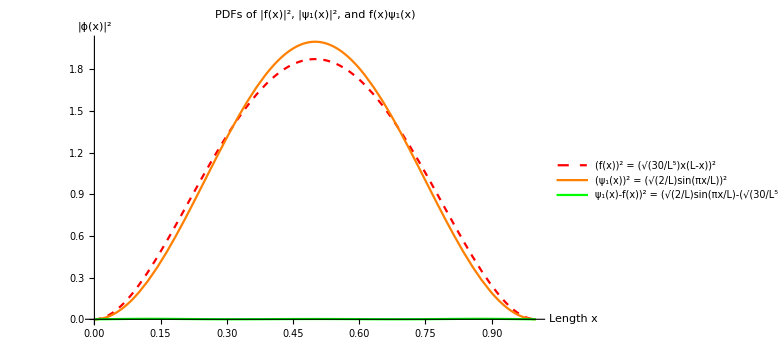

Calculate Probability Of x = 0 To x = L/3 For Each PDF |ϕ(x)|^2

(i)∫_0^(L/3) 2 Sin[π x]^2 = 1/3-(√3)/(4 π)

(ii)∫_0^(L/3) 30 (1-x)^2 x^2 = 17/81

(iii)∫_0^(L/3) (-√30 (1-x) x+√2 Sin[π x])^2 = 44/81-(4 √15)/π^3-(2 √5)/π^2+(-9+16 √5)/(12 √3 π)

---------------------------------------------
-----------------Question 4-----------------
---------------------------------------------

Solve for normalization constant A of initial PDF

(1) ∫_0^L ψψ^* = 1, then A^2∫_0^L (c_1ψ_1+c_2ψ_2)(c_1(ψ^*)_1+(c_2(ψ^*)_2)dx = 1.

(2) Expanding the integral in step 2, and using the fact that the
dot product of two orthonormal eigenstates is 0,
A^2[(1/4)^2∫_0^L ψ_1(ψ^*)_1dx + 0 + 0 + (3/4)^2∫_0^L ψ_2(ψ^*)_2dx] = 1

(3) Since ∫_0^L ψ_x(ψ^*)_xdx = 1, then A^2(1/16 +9/16) = 1. 
Therefore, A = √(16/10)= 4/(√10)

Plot initial PDF Of |ψ|^2 Where n=1, m=2, c_1=0.25, c_2=0.75, and A = 4/(√10)

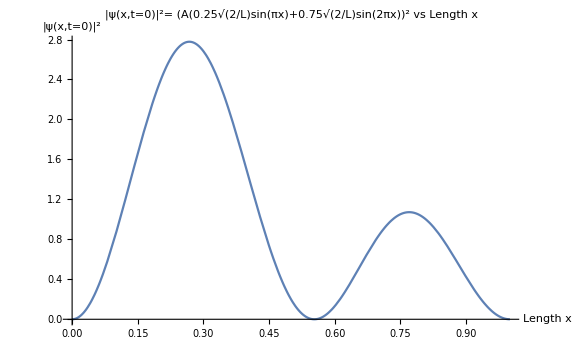

```mathematica
(*Particle-in-box-M4*)
(*Jared Frazier*)
(*Description:

Plot the probability density functions for the time-independent wave function
in one and two dimensions. Derive the expectation of position and momentum. 
Determine the normalization constants.

*)
(*Due: 10-12-2020*)

Clear["Global`*"];

(*-----------------------------*)
   (*1-1 => Plotting 1D PDFs*)
(*-----------------------------*)

Print["---------------------------------------------
-----------------Question 1-----------------
---------------------------------------------"
]

(*P(x) = Subscript[ψ, n](x) for n[1,3]*)
waveN1 := 2*(Sin[Pi*x])^2;
waveN2 := 2*(Sin[2*Pi*x])^2;
waveN3 := 2*(Sin[3*Pi*x])^2;

(*Plot these wave functions from a = 0, a = L where L = 1*)
Print["Probability Density Functions For |ψ_n(x)|^2 In 1D"]
Show[
	Plot[ 
		waveN1, 
		{x, 0, 1},
		PlotLabel->"|ψ_n(x)|^2 for n = 1,2,3" ,
		AxesLabel->{"Length x", "|ψ_n(x)|^2"},
		PlotStyle->{Red, Dashed},
		Filling->Axis,
		PlotLegends->{"ψ_1(x) = 2sin^2πx"}
	],
	Plot[
		waveN2, 
		{x, 0, 1},
		PlotStyle->{Green,Thick},
		Filling->Axis,
		PlotLegends->{"ψ_2(x) = 2sin^22πx"}
	],
	Plot[
		waveN3,
		{x,0,1},
		PlotRange->Full,
		Filling->Axis,
		PlotLegends->{"ψ_3(x) = 2sin^23πx"}
	]
]

(*-----------------------------*)
   (*1-2 => Plotting 2D PDFs*)
(*-----------------------------*)
Print["Density Functions for ψ_n(x)ψ_n(y)"]
(*2D wave functions for n=1,2,3,*)
waveN1X := Sqrt[2]*Sin[Pi*x];
waveN2X := Sqrt[2]*Sin[2*Pi*x];
waveN3X := Sqrt[2]*Sin[3*Pi*x];
waveN1Y := Sqrt[2]*Sin[Pi*y];
waveN2Y := Sqrt[2]*Sin[2*Pi*y];
waveN3Y := Sqrt[2]*Sin[2*Pi*y];
(*2D system*)
DensityPlot[
	waveN1X*waveN1Y,
	{x,0,1},
	{y,0,1},
	PlotLabel->"ψ_1(x)ψ_1(y) Density Plot"
]
DensityPlot[
	waveN2X*waveN2Y,
	{x,0,1},
	{y,0,1},
	PlotLabel->"ψ_2(x)ψ_2(y) Density Plot"
]
DensityPlot[
	waveN3X*waveN3Y,
	{x,0,1},
	{y,0,1},
	PlotLabel->"ψ_3(x)ψ_3(y)Density Plot"
]
(*-----------------------------*)
 (*2 => Expectation Derivation*)
(*-----------------------------*)
Print["---------------------------------------------
-----------------Question 2-----------------
---------------------------------------------"
]
(*Derive <x>*)
Print["Derive <x>"]
Print["(1) Steps 2-3 are the human intuition steps needed before Mathematica:"]
Print["(2) sin^2(nπx/L) =(1  -  cos (FractionBox[nπx, L]))/2 in the integrand of <x> = 2/L∫xsin^2(nπx/L)dx 
from the double angle identity"]
Print["(3) Then the sum of two integrals can be used to solve for <x> 
such that <x> =1/L[∫xdx + ∫cos(nπx/L)dx]"]
Print["(4) Given steps 2-3, I will use Mathematica to evaluate the integrals
∫xdx and ∫cos(nπx/L)dx] separately if 'n' is any positive integer on the interval
x = 0 to x = L"]
firstIntegral = Integrate[x, {x,0,L}]; (*Compute both integrals from 0 to L*)
secondIntegral = Assuming[
					Element[n, PositiveIntegers],
					Integrate[Cos[(n*Pi*x)/L], {x, 0, L}]
				  ];
Print["(5) From mathematica, '1/L * ", firstIntegral, " + ", secondIntegral, 
"' is <x>."]
Print["(6) <x> = L/2"]
Print[]

(*Derive <px>*)
Print["Derive <p_x>"]
Print["(1) Since (p̂)_x = -iℏd/dx, then <p_x> = -iℏ∫√(2/L)sin(nπx/L)d/dx√(2/L)sin(nπx/L)dx
simplifies to <p_x> = -iℏ(2  nπ)/L^2∫sin(nπx/L)cos(nπx/L)dx"]
expectationOfMomentum = Assuming [ (*Compute expectation of momentum*)
							Element[n, PositiveIntegers],
							Integrate[Sin[(n*Pi*x)/L]*Cos[(n*Pi*x)/L], {x, 0, L}]
						];
Print["(2) Using mathematica to evaluate the second integral from
step 1 on 
x = 0 to x = L where n is an element of the set of positive integers, then 
<p_x> = -iℏ(2  nπ)/L^2∫sin(nπx/L)cos(nπx/L) = -iℏ(2  nπ)/L^2*", expectationOfMomentum,
"\n(3) Therefore, <p_x> = 0"]
Print[]

(*Derive <x^2> for Subscript[σ^2, x]*)
Print["Derive <x^2> For (σ^2)_x "]
Print["(1) σ_x = √((σ^2)_x) = √(<SuperscriptBox[x, 2]> - <xSuperscriptBox[>, 2]). Therefore, I must derive <x^2> first
before calculating σ_x."]
Print["(2) <x^2> = 2/L∫x^2sin^2(nπx/L)dx, just like with <x> except now x^2
is in the integrand."]
Print["(3) sin^2(nπx/L) = (1  -  cos (FractionBox[nπx, L]))/2 so the integral in step 2 expands
to 1/L[∫x^2dx + ∫cos(nπx/L)dx]"]
Print["(4) From step 5 of the derivation of <x>, ∫cos(nπx/L)dx is zero
if n is an element of the set of positive integers."]
Print["(5) ∫x^2dx = ", Integrate[x^2, {x,0,L}], " so 1/L * ", Integrate[x^2, {x,0,L}]]
Print["(6) <x^2> = L^2/3"]
Print["(7) σ_x = √(σ_x^2) = √(<SuperscriptBox[x, 2]> - <xSuperscriptBox[>, 2]) = ", Sqrt[L^2/3 - L^2/4]] (*Subscript[σ, x]*)

(*Derive <Subscript[p, x]^2> for Subscript[σ^2, Subscript[p, x]]*)
Print[]
Print["Derive <p_x^2> For (σ^2)_p_x"]
Print["(1) σ_p_x = √(σ_p_x^2) = √(<SuperscriptBox[SubscriptBox[p, x], 2]> - <SubscriptBox[p, x]SuperscriptBox[>, 2]) and some human intuition is required
to set-up the proper integral, as in previous steps."]
Print["(2) This is the general expression
for  <p_x^2> = ∫√(2/L)sin(nπx/L)(-iℏd/dx(-iℏd/dx√(2/L)sin(nπx/L)))dx."]
Print["(3) Several constants in the expression can be pulled 
out of the integrand: (2 SuperscriptBox[i, 2] SuperscriptBox[ℏ, 2])/L∫sin(nπx/L)d^2/dx^2sin(nπx/L)dx"]
Print["(4) I will evaluate d^2/dx^2sin(nπx/L) in the integrand using Mathematica: ", 
Assuming[Element[n, PositiveIntegers], D[Sin[(n*Pi*x)/L] ,{x, 2}]]]
Print["(5) Then step 3 simplifies to -(2 SuperscriptBox[i, 2] SuperscriptBox[ℏ, 2] SuperscriptBox[n, 2] SuperscriptBox[π, 2])/L^3∫sin(nπx/L)sin(nπx/L)dx, the
integrand of which was already computed in step 5 of 'Derive <x>'
by using the double angle identity"]
Print["(6) Step 5, therefore, simplifies to -(2 SuperscriptBox[i, 2] SuperscriptBox[ℏ, 2] SuperscriptBox[n, 2] SuperscriptBox[π, 2])/L^3[∫xdx - ∫cos(nπx/L)], so
evaluating the second integral from x=0 to x=L using Mathematica, 
∫cos(nπx/L) = ", Assuming[Element[n, PositiveIntegers],
Integrate[Cos[(n*Pi*x)/L], {x, 0, L}]]]
Print["(7)Then all that's left is -(2 SuperscriptBox[i, 2] SuperscriptBox[ℏ, 2] SuperscriptBox[n, 2] SuperscriptBox[π, 2])/L^3∫xdx for x=0 to x=L,
and ∫xdx is simply ", Integrate[x, {x,0,L}]]
Print["(8) <p_x^2> = ",  (2 ℏ^2 n^2 π^2)/L^3 * Integrate[x, {x,0,L}]]
Print["(9) Then σ_p_x = √(σ_p_x^2) = √(<SuperscriptBox[SubscriptBox[p, x], 2]> - <SubscriptBox[p, x]SuperscriptBox[>, 2]) = ", Sqrt[(2 ℏ^2 n^2 Pi^2)/L^3 * Integrate[x, {x,0,L}]]]

(*-----------------------------*)
(*3 => Acceptable wave function*)
(*-----------------------------*)
Print["---------------------------------------------
-----------------Question 3-----------------
---------------------------------------------"
]
(*Find normalization constant*)
Print["Find Normalization Constant 'A'"]
Print["(1) f(x) is normal if ∫f(x)f(x)dx = 1. Therefore,
I can solve for A from ∫A^2[x(x-L)(x-L)]dx = 1 since 'A' is a constant."]
Print["(2) A^2" , Integrate[(x*(x-L))^2, {x, 0, L}], " = 1"]
Print["(3) f(x) is normalized if A = ", Sqrt[1/(Integrate[(x*(x-L))^2, {x, 0, L}])]]
Print["(4) A = √(30/L^5)"]

Print[]
(*Plot f(x) with exact ground state wave function assuming L = 1*)
Print["Plot the PDFs assuming L = 1"]
L = 1;
groundStateWaveFunc = Sqrt[2/L]*Sin[(Pi*x)/L];
fx = Sqrt[30/L^5]*x*(L-x);
Show[
	Plot[ (*Plot fx squared*)
		(fx)^2,
		{x, 0, L},
		PlotRange->All,
		PlotLabel->"PDFs of |f(x)|^2, |ψ_1(x)|^2, and f(x)ψ_1(x)",
		AxesLabel->{"Length x","|ϕ(x)|^2"},
		PlotLegends->{"(f(x))^2 = (√(30/L^5)x(L-x))^2"},
		PlotStyle->{Red, Dashed},
		ImageSize->Large
	],
	Plot[ (*Plot the ground state wave function squared*)
		(groundStateWaveFunc)^2,
		{x, 0, L},
		PlotLegends->{"(ψ_1(x))^2 = (√(2/L)sin(πx/L))^2"},
		PlotStyle->{Orange, Bold}
	],
	Plot[ (*Plot difference between fx and ground state then square it*)
		(groundStateWaveFunc-fx)^2,
		{x, 0, L},
		PlotLegends->{"ψ_1(x)-f(x))^2 = (√(2/L)sin(πx/L)-(√(30/L^5)x(L-x))^2"},
		PlotStyle->{Green, Thick}
	]
]

(*Probability calculations for each PDF*)
Print["Calculate Probability Of x = 0 To x = L/3 For Each PDF |ϕ(x)|^2"]
probGroundState = Integrate[groundStateWaveFunc^2, {x, 0, L/3}];
probFx = Integrate[fx^2, {x, 0, L/3}];
probProduct = Integrate[(groundStateWaveFunc-fx)^2, {x, 0, L/3}];
Print["(i)∫_0^(L/3) ",groundStateWaveFunc^2, " = ", probGroundState]
Print["(ii)∫_0^(L/3) ",fx^2, " = ", probFx]
Print["(iii)∫_0^(L/3) ", (groundStateWaveFunc-fx)^2, " = ", probProduct]
Print[]
(*-----------------------------*)
 (*4 => Superposition*)
(*-----------------------------*)
Print["---------------------------------------------
-----------------Question 4-----------------
---------------------------------------------"
]
Print["Solve for normalization constant A of initial PDF"]
Print["(1) ∫_0^L ψψ^* = 1, then A^2∫_0^L (c_1ψ_1+c_2ψ_2)(c_1(ψ^*)_1+(c_2(ψ^*)_2)dx = 1."]
Print["(2) Expanding the integral in step 2, and using the fact that the
dot product of two orthonormal eigenstates is 0,
A^2[(1/4)^2∫_0^L ψ_1(ψ^*)_1dx + 0 + 0 + (3/4)^2∫_0^L ψ_2(ψ^*)_2dx] = 1"]
Print["(3) Since ∫_0^L ψ_x(ψ^*)_xdx = 1, then A^2(1/16 +9/16) = 1. 
Therefore, A = √(16/10)= 4/(√10)"]
Print[]
(*Plot Initial PDFs*)
normConstA = 4/Sqrt[10];
Print["Plot initial PDF Of |ψ|^2 Where n=1, m=2, c_1=0.25, c_2=0.75, and A = 4/(√10)"]
Plot[
	(normConstA*(0.25*waveN1X+0.75*waveN2X))^2, 
	{x, 0, L}, 
	PlotRange->All, 
	PlotLabel->"|ψ(x,t=0)|^2= (A(0.25√(2/L)sin(πx)+0.75√(2/L)sin(2πx))^2 vs Length x",
	AxesLabel->{"Length x","|ψ(x,t=0)|^2"},
	ImageSize->Large
]
```